## SSS1. Expressions, Functions, and Boolean Logic

## Table of Contents

A. Lab
	Data Types-Continuation
		Associations
	Pure Functions
B. Topic- Complex Systems
C. Exercises

## A. Lab

### Data Types-Continuation

#### Associations

Associations are a data type consisting of keys and values associated with them.

```mathematica
assoc=<|b-> 1,d->3,c-> 2,a->4|>;
```

accessing an element (make sure you run the line above so the assoc is defined.

```mathematica
assoc[b]
```

extracting all the keys from the association

```mathematica
Keys[assoc]
```

extracting all values in the association

```mathematica
Values[assoc]
```

testing whether a key exists

```mathematica
KeyExistsQ[assoc,f]
```

Sort sorts the association by values

```mathematica
Sort[assoc]
```

KeySort by keys

```mathematica
KeySort[assoc]
```

Alternative ways of creating an association:

Grouping a list of elements by a certain criterion

```mathematica
GroupBy[{"ich","du","er","sie","es"},StringLength]
```

Inputting a list of keys and values

```mathematica
AssociationThread[{a,b,c,d,e}->{1,2,3,4,5}]
```

apply a function to a list of keys:

```mathematica
AssociationMap[#^2&,Range[10]]
```

### Pure Functions

AssociationMap[#^2&,Range[10]] is an example of how to use the pure function (#^2&). Pure functions let you make a general form of a function where you can substitute in values multiple times without having to actually define the function with the function[input_]:=... syntax.  
#^2& is equivalent to square[a_]:=a^2, but won’t be saved.

Another example of using a pure function

```mathematica
Map[#^2&,{1,2,5,1,42,4}]
```

An alternative syntax for Map, can you see what is going on?

```mathematica
#^2&/@{1,2,5,1,42,4}
```

Can you predict what the following code does?

```mathematica
Select[Range[10],#<6&]
```

You can also use more than one placeholder in your pure function. The following code is  comparing two elements by a certain criterion and sorting the entire list like that.

```mathematica
Sort[Range[10],#1>#2&]
```

Your turn: Look up the documentation for at least one of the following functions. Find an example using pure functions, then make your own below: SortBy, GroupBy, Nest/NestList, Fold/FoldList MaximalBy

## B. Topic- Complex Systems

### Graphs and Networks

In your complex systems class last semester you were looking at graphs, their connectivity, etc. Wolfram has a nice way of displaying and analysing some of these computationally. 
Instead of a,b,c, let’s use some real-life data for our example. ExampleData gives you access to a number of datasets. Let’s look at the number of times each character in the play “Les Miserables” appears in combination with another character. The graph is undirected but the edges have weight that represent the number of times the characters appear together.

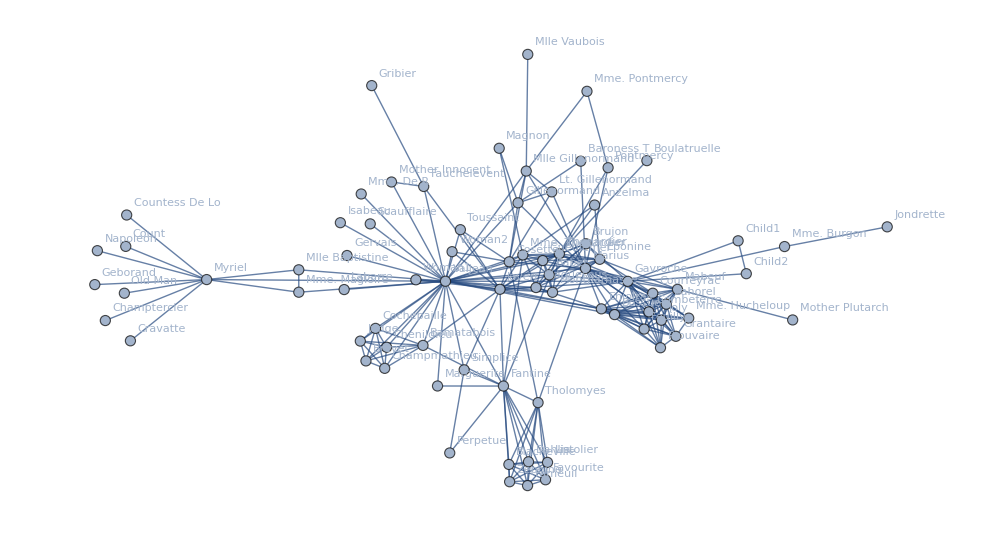

```mathematica
g=Graph[ExampleData[{"NetworkGraph","LesMiserables"}],VertexLabels->"Name"]
```

We could analyze the network as a social network with CommunityGraphPlot. The function groups the network into different communities

```mathematica
CommunityGraphPlot[g]
```

-Graphics-

AssociationThread takes as input two lists and makes an association from the first to the second. Let’s take the names of the characters and connect them to their “BetweennessCentrality”. This number measures how many of the paths from one person to the other have to go through the node in question (they are not integers in this case, because of the weighted graph). 
Do you think this is a good measure of how important the character is for the book?

```mathematica
AssociationThread[VertexList[g],BetweennessCentrality[g]]//Sort
```

<|Napoleon→0.,Mlle Baptistine→0.,Mme. Magloire→0.,Countess De Lo→0.,Geborand→0.,Champtercier→0.,Cravatte→0.,Count→0.,Old Man→0.,Labarre→0.,Marguerite→0.,Mme. De R→0.,Isabeau→0.,Gervais→0.,Listolier→0.,Fameuil→0.,Blacheville→0.,Favourite→0.,Dahlia→0.,Zephine→0.,Perpetue→0.,Scaufflaire→0.,Woman1→0.,Judge→0.,Champmathieu→0.,Brevet→0.,Chenildieu→0.,Cochepaille→0.,Boulatruelle→0.,Anzelma→0.,Woman2→0.,Mother Innocent→0.,Gribier→0.,Jondrette→0.,Mlle Vaubois→0.,Lt. Gillenormand→0.,Baroness T→0.,Prouvaire→0.,Mother Plutarch→0.,Toussaint→0.,Child1→0.,Child2→0.,Mme. Hucheloup→0.,Grantaire→0.428571,Magnon→0.619048,Mme. Pontmercy→1.,Brujon→1.25,Combeferre→3.56291,Feuilly→3.56291,Bahorel→6.22864,Joly→6.22864,Montparnasse→11.0404,Claquesous→13.8561,Gueulemer→14.1371,Babet→14.1371,Courfeyrac→15.011,Pontmercy→19.7375,Bamatabois→22.9167,Simplice→24.6248,Eponine→32.7395,Gillenormand→57.6003,Cosette→67.8193,Mme. Burgon→75.,Fauchelevent→75.5,Mabeuf→78.8345,Mme. Thenardier→82.6569,Bossuet→87.6479,Tholomyes→115.794,Enjolras→121.277,Mlle Gillenormand→135.657,Javert→154.845,Thenardier→213.468,Fantine→369.487,Marius→376.293,Gavroche→470.571,Myriel→504.,Valjean→1624.47|>

Another topic we talked about in class is the degree of each vertex. This is a measure of how many other nodes are connected to the vertex.

```mathematica
AssociationThread[VertexList[g],VertexDegree[g]]//Sort
```

<|Napoleon→1,Countess De Lo→1,Geborand→1,Champtercier→1,Cravatte→1,Count→1,Old Man→1,Labarre→1,Mme. De R→1,Isabeau→1,Gervais→1,Scaufflaire→1,Boulatruelle→1,Gribier→1,Jondrette→1,Mlle Vaubois→1,Mother Plutarch→1,Marguerite→2,Perpetue→2,Woman1→2,Mother Innocent→2,Mme. Burgon→2,Magnon→2,Mme. Pontmercy→2,Baroness T→2,Child1→2,Child2→2,Mlle Baptistine→3,Mme. Magloire→3,Pontmercy→3,Anzelma→3,Woman2→3,Toussaint→3,Fauchelevent→4,Simplice→4,Lt. Gillenormand→4,Judge→6,Champmathieu→6,Brevet→6,Chenildieu→6,Cochepaille→6,Listolier→7,Fameuil→7,Blacheville→7,Favourite→7,Dahlia→7,Zephine→7,Gillenormand→7,Mlle Gillenormand→7,Brujon→7,Mme. Hucheloup→7,Bamatabois→8,Tholomyes→9,Prouvaire→9,Montparnasse→9,Myriel→10,Grantaire→10,Gueulemer→10,Babet→10,Claquesous→10,Mme. Thenardier→11,Cosette→11,Eponine→11,Mabeuf→11,Combeferre→11,Feuilly→11,Bahorel→12,Joly→12,Courfeyrac→13,Bossuet→13,Fantine→15,Enjolras→15,Thenardier→16,Javert→17,Marius→19,Gavroche→22,Valjean→36|>

The GraphDensity is a measure of the connectivity of a graph. It is computed by taking the (number of edges)/(number of possible edges)

```mathematica
GraphDensity[g]//N
```

0.0868079

## C. Exercises

Euler, Gauss, Archimedes, Pascal, Ramanujan, Hardy, Bernoulli, Cantor, and Leibniz form a friend group. Come up with at least 10 (directed) connections of whom likes whom and create a Graph and CommunityGraphPlot.

```mathematica
m=Graph[{"Euler"->"Pascal","Ramanujan"-> "Hardy","Hardy"-> "Ramanujan",(*...your one-sided friendships go here*)},VertexLabels->"Name"]
```

How do you think you could use these graphs for Complex Systems projects in the future? Come up with at least one example.

Select the Vertexes in the LesMiserable graph that have more than 5 co-occurences